## Functions

## Expected photon number

```mathematica
Heaviside[x_]:=Which[x<0,0,x==0,1,x>0,1]
Ef[t_,x_,S_]:=∑_(i=1)^Length[S] Heaviside[t-S[[i]]] ⅇ^(x S[[i]])
nom[t_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_]:=(α1^(2 Ef[t,0,tr]+2)ⅇ^(α1^2 ⅇ^(-γ t))+ⅇ^(-Abs[β2-β1]^2/2)ⅇ^(ⅈ Im[Conjugate[β1]β2+g/ω(β2-β1)(Ef[t,-ⅈ ω,tr]-Ef[t,0,tr] ⅇ^(-ⅈ ω t))])(α1 α2 ⅇ^(- ⅈ g/ω Im[(β2-β1)(1-ⅇ^(-ⅈ ω t))]))^(Ef[t,0,tr]+1)ⅇ^(α1 α2 ⅇ^(-γ t)  ⅇ^(- ⅈ g/ω Im[(β2-β1)(1-ⅇ^(-ⅈ ω t))])));
deno[t_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_]:=(α1^(2 Ef[t,0,tr])ⅇ^(α1^2 ⅇ^(-γ t))+ⅇ^(-Abs[β2-β1]^2/2)ⅇ^(ⅈ Im[Conjugate[β1]β2+g/ω(β2-β1)(Ef[t,-ⅈ ω,tr]-Ef[t,0,tr] ⅇ^(-ⅈ ω t))])(α1 α2 ⅇ^(- ⅈ g/ω Im[(β2-β1)(1-ⅇ^(-ⅈ ω t))]))^Ef[t,0,tr] ⅇ^(α1 α2 ⅇ^(-γ t)  ⅇ^(- ⅈ g/ω Im[(β2-β1)(1-ⅇ^(-ⅈ ω t))])));
n[t_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_]:=ⅇ^(-γ t)*((nom[t,γ,α1,α2,β1,β2,tr,g,ω]+nom[t,γ,α2,α1,β2,β1,tr,g,ω])/(deno[t,γ,α1,α2,β1,β2,tr,g,ω]+deno[t,γ,α2,α1,β2,β1,tr,g,ω]));
```

## Probability distribution g

```mathematica
ProbDistg[t_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_,p_,dg_,gmax_]:={tab=Table[{x,p[x] ⅇ^(-NIntegrate[n[t0,γ,α1,α1,β1,β2,tr,x,ω],{t0,0,t}])∏_(j=1)^Length[Select[tr,#≤t&]] n[tr[[j]],γ,α1,α1,β1,β2,tr,x,ω]},{x,0,gmax,dg}];
tabnorm=Transpose[{Transpose[tab][[1]],(Transpose[tab][[2]])/(Total[tab][[2]]*dg)}]}[[1]]
ProbDistg3d[t_,dt_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_,p_,dg_,gmax_]:={ 
table=Table[Transpose[ProbDistg[t0,γ,α1,α2,β1,β2,tr,g,ω,p,dg,gmax]][[2]],{t0,0,t,dt}];
plot3d=(*ListDensityPlot[table,DataRange->{{0,gmax},{0,t}},InterpolationOrder->1,ColorFunctionScaling->False,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed"];*)
MatrixPlot[table,AspectRatio->1,DataRange->{{0,gmax},{0,t}},ColorFunctionScaling->False,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed",DataReversed->True];
exp=Table[table[[t0]].Table[x,{x,0,gmax,dg}]*dg,{t0,1,Length[table]}];
var=Table[√(table[[t0]].Table[x^2,{x,0,gmax,dg}]*dg-exp[[t0]]^2),{t0,1,Length[table]}];
Lplot=ListPlot[{
Transpose[{Table[t0,{t0,0,t,dt}],exp+var}],
Transpose[{Table[t0,{t0,0,t,dt}],exp}],
Transpose[{Table[t0,{t0,0,t,dt}],exp-var}]
},PlotStyle->{{Dashed,Black},{Opacity[0.7]},{Dashed,Black}},Filling->{1->{3}},FillingStyle->{LightOrange},Joined->True,InterpolationOrder->2,PlotTheme->"Detailed",PlotRange->{{0,t},{0,gmax}}];{plot3d,Lplot}}[[1]]
```

## Probability distribution ω

```mathematica
ProbDistω[t_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_,p_,dω_,ωmax_,ωmin_]:={tab=Table[{x,p[x] ⅇ^(-NIntegrate[n[t0,γ,α1,α1,β1,β2,tr,g,x],{t0,0,t}])∏_(j=1)^Length[Select[tr,#≤t&]] n[tr[[j]],γ,α1,α1,β1,β2,tr,g,x]},{x,ωmin,ωmax,dω}];
tabnorm=Transpose[{Transpose[tab][[1]],(Transpose[tab][[2]])/(Total[tab][[2]]*dω)}]}[[1]]
ProbDistω3d[t_,dt_,γ_,α1_,α2_,β1_,β2_,tr_,g_,ω_,p_,dω_,ωmax_,ωmin_]:={ 
table=Table[Transpose[ProbDistω[t0,γ,α1,α2,β1,β2,tr,g,ω,p,dω,ωmax,ωmin]][[2]],{t0,0,t,dt}];
plot3d=(*ListDensityPlot[table,DataRange->{{0,ωmax},{0,t}},InterpolationOrder->1,ColorFunctionScaling->False,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed"];*)
MatrixPlot[table,AspectRatio->1,DataRange->{{ωmin,ωmax},{0,t}},ColorFunctionScaling->False,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed",DataReversed->True];
exp=Table[table[[t0]].Table[x,{x,ωmin,ωmax,dω}]*dω,{t0,1,Length[table]}];
var=Table[√(table[[t0]].Table[x^2,{x,ωmin,ωmax,dω}]*dω-exp[[t0]]^2),{t0,1,Length[table]}];
Lplot=ListPlot[{
Transpose[{Table[t0,{t0,0,t,dt}],exp+var}],
Transpose[{Table[t0,{t0,0,t,dt}],exp}],
Transpose[{Table[t0,{t0,0,t,dt}],exp-var}]
},PlotStyle->{{Dashed,Black},{Opacity[0.7]},{Dashed,Black}},Filling->{1->{3}},FillingStyle->{LightOrange},Joined->True,InterpolationOrder->2,PlotTheme->"Detailed",PlotRange->{{0,t},{ωmin,ωmax}}];{plot3d,Lplot}}[[1]]
```

## Parameter Estimation

## g estimation

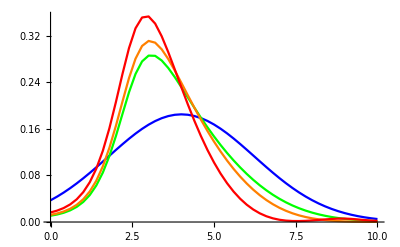

```mathematica
tr={1,6,13.2};
p[x_]:=1 ⅇ^(-0.1(x-4)^2)
a1=ListPlot[ProbDistg[0.1,0.5,2,2,1,1.2,tr,1,0.5,p,0.2,10],PlotStyle->Blue,Joined->True,PlotRange->All];
a2=ListPlot[ProbDistg[5  ,0.5,2,2,1,1.2,tr,1,0.5,p,0.2,10],PlotStyle->Green,Joined->True,PlotRange->All];
a4=ListPlot[ProbDistg[10  ,0.5,2,2,1,1.2,tr,1,0.5,p,0.2,10],PlotStyle->Orange,Joined->True,PlotRange->All];
a5=ListPlot[ProbDistg[20,0.5,2,2,1,1.2,tr,1,0.5,p,0.2,10],PlotStyle->Red,Joined->True,PlotRange->All];
Show[a1,a2,a4,a5,PlotRange->All,PlotRange->{{0,10},{0,1}}]
```

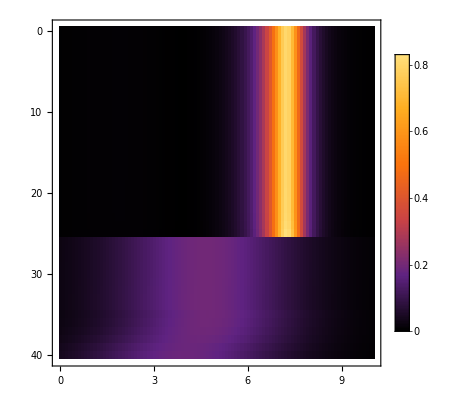
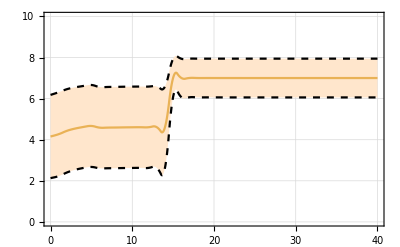

```mathematica
tr={3,20,40};
p[x_]:=1 ⅇ^(-0.1(x-4)^2)
pp=ProbDistg3d[40,1,0.5,1,1,1,1.2,{8,15},1,0.5,p,0.1,10]
```

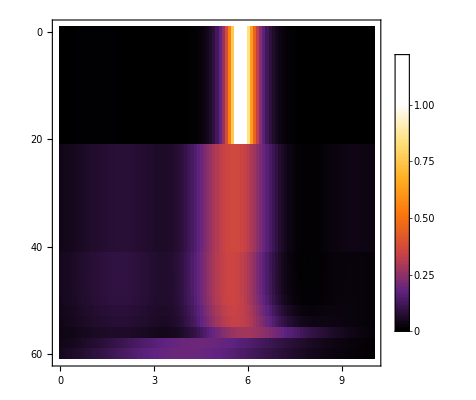
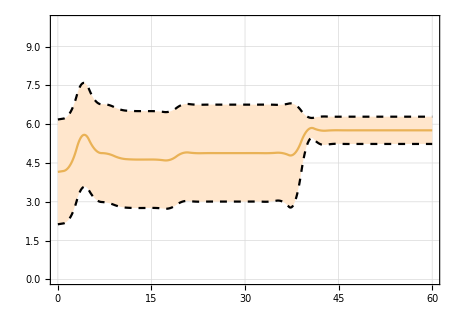

```mathematica
tr={3,20,40};
p[x_]:=1 ⅇ^(-0.1(x-4)^2)
pp=ProbDistg3d[60,2,0.5,1,1,1,1.2,{3,20,40},1,0.5,p,0.1,10]
```

```mathematica
pp2=ProbDistg3d[60,3,0.5,1,1,1,2,{5,50},1,1,p,0.2,10]
```

```mathematica
p[x_]:=ⅇ^(-2(x-4)^2)
pp2=ProbDistg3d[60,3,1,1,1,1,10,{10,30},1,1,p,0.2,10]
```

```mathematica
p[x_]:=1
pp3=ProbDistg3d[60,1,1,1,1,1,10,{10},1,1,p,0.2,10]
```

## ω estimation

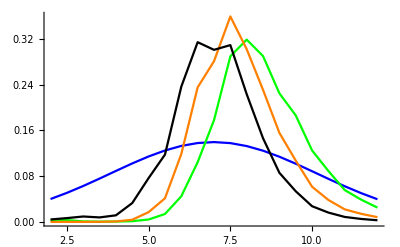

```mathematica
tr={1,3,20};
p[x_]:=1 ⅇ^(-0.05(x-7)^2)
a1=ListPlot[ProbDistω[0.1,0.1,5,5,1,2,tr,1,1,p,0.5,12,2],PlotStyle->Blue,Joined->True,PlotRange->All];
a2=ListPlot[ProbDistω[5    ,0.1,5,5,1,2,tr,1,1,p,0.5,12,2],PlotStyle->Green,Joined->True,PlotRange->All];
a4=ListPlot[ProbDistω[10  ,0.1,5,5,1,2,tr,1,1,p,0.5,12,2],PlotStyle->Orange,Joined->True,PlotRange->All];
a5=ListPlot[ProbDistω[20  ,0.1,5,5,1,2,tr,1,1,p,0.5,12,2],PlotStyle->Red,Joined->True,PlotRange->All];
a5=ListPlot[ProbDistω[80  ,0.1,5,5,1,2,tr,1,1,p,0.5,12,2],PlotStyle->Black,Joined->True,PlotRange->All];
Show[a1,a2,a4,a5,PlotRange->All,PlotRange->{{0,10},{0,1}}]
```

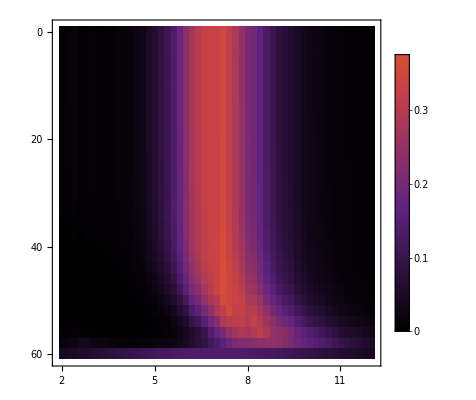
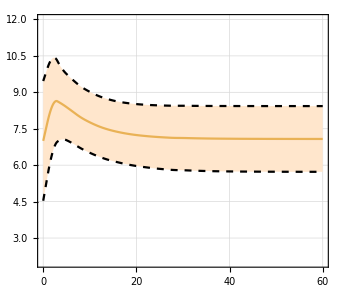

```mathematica
p[x_]:=1 ⅇ^(-0.05(x-7)^2)
pp=ProbDistω3d[60,2,0.1,5,5,1,2,{3,10,30},1,1,p,0.2,12,2]
```

```mathematica
N[25*ⅇ^(-12*0.3)* (1-ⅇ^(-0.2^2/2))/(1+ⅇ^(-0.2^2/2))]
```

0.0068307

## cyclic nature of k parameter

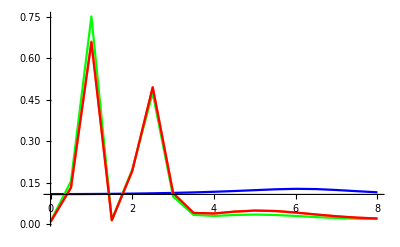

```mathematica
tr={3,6,12};
p[x_]:=1(*ⅇ^(-0.03(x-10)^2)*)
a1=ListPlot[ProbDistg[0.1,0.3,5,5,1,1.2,tr,1,1,p,0.5,8],PlotStyle->Blue,Joined->True,PlotRange->All];
a2=ListPlot[ProbDistg[10  ,0.3,5,5,1,1.2,tr,1,1,p,0.5,8],PlotStyle->Green,Joined->True,PlotRange->All];
a4=ListPlot[ProbDistg[20  ,0.3,5,5,1,1.2,tr,1,1,p,0.5,8],PlotStyle->Orange,Joined->True,PlotRange->All];
a5=ListPlot[ProbDistg[40,0.3,5,5,1,1.2,tr,1,1,p,0.5,8],PlotStyle->Red,Joined->True,PlotRange->All];
Show[a1,a2,a4,a5,PlotRange->All,PlotRange->{{0,10},{0,1}}]
```

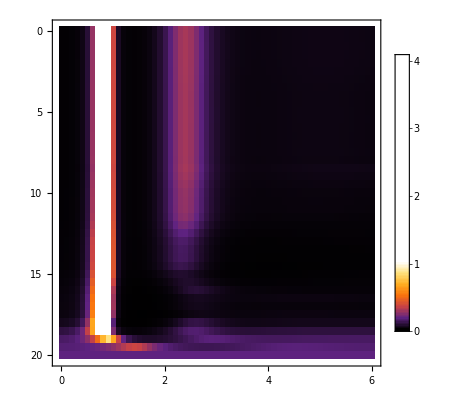
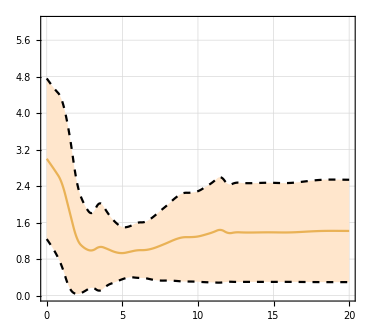

```mathematica
tr={3,6,12};
p[x_]:=1
pp=ProbDistg3d[20,0.5,0.3,5,5,1,1.2,{3,6,12},1,1,p,0.1,6]
```

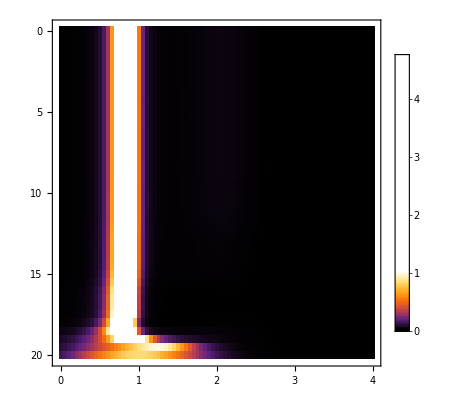
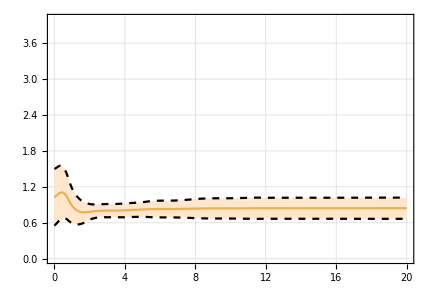

```mathematica
tr={3,6,12};
p[x_]:=ⅇ^(-2(x-1)^2)
pp=ProbDistg3d[20,0.5,0.3,5,5,1,1.2,{3,6,12},1,1,p,0.05,4]
```